# Dynamic Bar PDE

### A, ρ, E, f(x, t), Domain, BCs and/or ICs

```mathematica
ClearAll[u,A,Ê,ρ,f,pde,disp,L,Period]
myResults="test.json";
myPath="C:\\Users\\itopo\\Documents\\Marina\\NeuralNetwork-Project\\";
```

-Graphics3D-

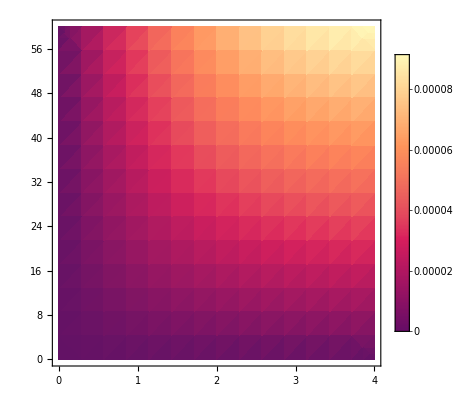

```mathematica
L=4.;
Period=60.0;
A=0.5;
Ê=210*10^9;
ρ=7850.0;
f=20000*t;
source="Polynomial";
elasticity=Ê;
conditions={"u_x0"->0.0,"u_t0"->0.0}; (*{"u_x0"->,"u_xL"->,"u_t0"->,"du_xL"->}*)
pde=ρ A D[D[u[x,t],t],t]-D[Ê A D[u[x,t],x],x]==f;
sol1=NDSolve[{pde,u[0,t]==0,u[x,0]==0},u[x,t],{x,0,L},{t,0,Period}];
disp[x_,t_]=u[x,t]/. sol1[[1]];
Plot3D[disp[x,t],{x,0,L},{t,0,Period}]
DensityPlot[disp[x,t],{x,0,L},{t,0,Period},PlotLegends->Automatic]
```

### Organize Data

```mathematica
properties={"L"->L,"Interval"->Period,"A"->A,"E"->elasticity,"rho"->ρ,"f"->source};
nXpts=200;
nTpts=200;

posis=Table[0,{i,1,nXpts}];
times=Table[0,{i,1,nTpts}];
posis=Range[0.0,L,L/(nXpts-1)];
times=Range[0.0,Period,Period/(nTpts-1)];
points=Table[0,{i,1,nXpts},{j,1,nTpts}];
points=Table[disp[posis[[i]],times[[j]]],{i,1,nXpts},{j,1,nTpts}];
```

### Export Data

```mathematica
data={"Properties"->properties,"BCs_ICs"->conditions,"x"->posis,"t"->times,"u"->points};

Export[myPath<>myResults,data,"JSON"];
```